```mathematica
myData[n_] := ReadList[StringJoin["d:\\Triangle\\DataSrc\\Summary_UpTo_",ToString[n],".txt"],Number, RecordLists->True ]
```

```mathematica
magic[primeList_] :=magic[primeList]=N[(∏_p^primeList (1/p+1)^(1/(log(p))))/(2^(∑_p^primeList 1/(log(p))))]
```

```mathematica
magicGraham(primeList_):=∑_p^primeList (log((p+1)/(2 p)))/(log(p))+1
```

```mathematica
myFormula[a_,b_,c_,d_] := N[  2^(-(1/Log[a]+1/Log[b]+1/Log[c]+1/Log[d])) (1+1/a)^(1/Log[a]) (1+1/b)^(1/Log[b]) (1+1/c)^(1/Log[c]) (1+1/d)^(1/Log[d]) ]
```

```mathematica
formulaTable[l_] := Sort[
Table[{N[magicGraham[{x[[1]]  ,x[[2]],x[[3]],x[[4]]}]],
 x[[5]] },{x,l}]]
```

```mathematica
huge = myData[20]
```

{{3,5,7,11,3},{3,5,7,13,5},{3,5,7,17,2},{3,5,7,19,3},{3,5,7,23,4},{3,5,7,29,3},{3,5,7,31,3},{3,5,7,37,6},{3,5,7,41,7},{3,5,7,43,3},{3,5,7,47,8},{3,5,7,53,10},{3,5,7,59,5},{3,5,7,61,7},{3,5,7,67,5},{3,5,7,71,6},{3,5,7,73,6},{3,5,7,79,4},{3,5,7,83,12},{3,5,7,89,4},{3,5,7,97,5},{3,5,11,13,4},{3,5,11,17,10},{3,5,11,19,3},{3,5,11,23,9},{3,5,11,29,12},{3,5,11,31,13},{3,5,11,37,9},«10570»,{67,71,83,89,22803},{67,71,83,97,40477},{67,71,89,97,21701},{67,73,79,83,23895},{67,73,79,89,26180},{67,73,79,97,22986},{67,73,83,89,16217},{67,73,83,97,21072},{67,73,89,97,16937},{67,79,83,89,16608},{67,79,83,97,34077},{67,79,89,97,23502},{67,83,89,97,31626},{71,73,79,83,28583},{71,73,79,89,23125},{71,73,79,97,25081},{71,73,83,89,20988},{71,73,83,97,26315},{71,73,89,97,31022},{71,79,83,89,19081},{71,79,83,97,36344},{71,79,89,97,22721},{71,83,89,97,24355},{73,79,83,89,19336},{73,79,83,97,33611},{73,79,89,97,22458},{73,83,89,97,22663},{79,83,89,97,45085}}

```mathematica
Sum[huge[[i]][[5]],{i,1,Length[huge]}]
```

252433

```mathematica
myFormulaInv[a_,b_,c_,d_] := N[  2^(1/Log[a]+1/Log[b]+1/Log[c]+1/Log[d])/ (1+1/a)^(1/Log[a]) (1+1/b)^(1/Log[b]) (1+1/c)^(1/Log[c]) (1+1/d)^(1/Log[d]) ]
```

```mathematica
formulaValues =Sort[ Table[{myFormula[x[[1]]  ,x[[2]],x[[3]],x[[4]]], x[[5]] ,x},{x,huge}]]
```

{{0.293221,3,{3,5,7,11,3}},{0.296593,5,{3,5,7,13,5}},{0.301639,2,{3,5,7,17,2}},{0.303602,3,{3,5,7,19,3}},{0.307098,4,{3,5,11,13,4}},{0.312323,10,{3,5,11,17,10}},{0.314355,3,{3,5,11,19,3}},{0.315914,4,{3,5,13,17,4}},{0.31639,4,{3,7,11,13,4}},{0.31797,8,{3,5,13,19,8}},{0.321773,9,{3,7,11,17,9}},{0.32338,2,{3,5,17,19,2}},{0.323867,7,{3,7,11,19,7}},{0.325472,5,{3,7,13,17,5}},{0.327591,12,{3,7,13,19,12}},{0.333164,8,{3,7,17,19,8}},{0.33317,8,{5,7,11,13,8}},{0.337001,11,{3,11,13,17,11}},{0.338838,12,{5,7,11,17,12}},{0.339194,18,{3,11,13,19,18}},{0.341043,11,{5,7,11,19,11}},{0.342734,10,{5,7,13,17,10}},{0.344965,16,{5,7,13,19,16}},{0.344965,13,{3,11,17,19,13}},{0.348931,40,{3,13,17,19,40}},{0.350833,8,{5,7,17,19,8}},{0.354874,21,{5,11,13,17,21}},{0.357183,21,{5,11,13,19,21}},{0.36326,61,{5,11,17,19,61}},{0.365611,102,{7,11,13,17,102}},{0.367437,268,{5,13,17,19,268}},{0.367991,55,{7,11,13,19,55}},{0.374251,596,{7,11,17,19,596}},{0.378554,6620,{7,13,17,19,6620}},{0.391963,244453,{11,13,17,19,244453}}}

```mathematica
formulaTable[myData[20]]
```

{{0.293221,3},{0.296593,5},{0.301639,2},{0.303602,3},{0.307098,4},{0.312323,10},{0.314355,3},{0.315914,4},{0.31639,4},{0.31797,8},{0.321773,9},{0.32338,2},{0.323867,7},{0.325472,5},{0.327591,12},{0.333164,8},{0.33317,8},{0.337001,11},{0.338838,12},{0.339194,18},{0.341043,11},{0.342734,10},{0.344965,16},{0.344965,13},{0.348931,24},{0.350833,8},{0.354874,15},{0.357183,10},{0.36326,46},{0.365611,56},{0.367437,44},{0.367991,22},{0.374251,103},{0.378554,76},{0.391963,397}}

Part::partw: Part {3} of {{-0.22682794141729878`, 0.38888375226122973`}, {0.6931471805599453`, 10.716304875934007`}} does not exist.

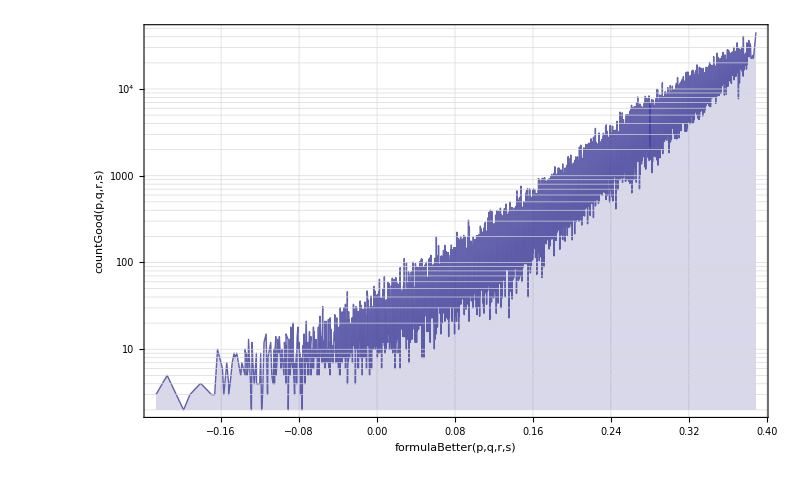

```mathematica
ListLogPlot[{formulaTable[myData[10]]}, 
			GridLines->Automatic,
                             PlotRange->All,
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
                              Ticks->{All,All,All},  
                              PerformanceGoal->"Quality", 
                              Method->"QuasiNewton",
                              ImageSize->Large,
                              PlotStyle->Opacity[0.8],
                              Joined->True,
                             Filling->Axis,
                             Frame->True,
			 AxesLabel->{"formulaBetter(p,q,r,s)","countGood(p,q,r,s)"}
                               ]
```

```mathematica
Sort[formulaValues]
```

{{0.293221,3,{3,5,7,11,3}},{0.296593,5,{3,5,7,13,5}},{0.301639,2,{3,5,7,17,2}},{0.303602,3,{3,5,7,19,3}},{0.307098,4,{3,5,11,13,4}},{0.312323,10,{3,5,11,17,10}},{0.314355,3,{3,5,11,19,3}},{0.315914,4,{3,5,13,17,4}},{0.31639,4,{3,7,11,13,4}},{0.31797,8,{3,5,13,19,8}},{0.321773,9,{3,7,11,17,9}},{0.32338,2,{3,5,17,19,2}},{0.323867,7,{3,7,11,19,7}},{0.325472,5,{3,7,13,17,5}},{0.327591,12,{3,7,13,19,12}},{0.333164,8,{3,7,17,19,8}},{0.33317,8,{5,7,11,13,8}},{0.337001,11,{3,11,13,17,11}},{0.338838,12,{5,7,11,17,12}},{0.339194,18,{3,11,13,19,18}},{0.341043,11,{5,7,11,19,11}},{0.342734,10,{5,7,13,17,10}},{0.344965,16,{5,7,13,19,16}},{0.344965,13,{3,11,17,19,13}},{0.348931,40,{3,13,17,19,40}},{0.350833,8,{5,7,17,19,8}},{0.354874,21,{5,11,13,17,21}},{0.357183,21,{5,11,13,19,21}},{0.36326,61,{5,11,17,19,61}},{0.365611,102,{7,11,13,17,102}},{0.367437,268,{5,13,17,19,268}},{0.367991,55,{7,11,13,19,55}},{0.374251,596,{7,11,17,19,596}},{0.378554,6620,{7,13,17,19,6620}},{0.391963,244453,{11,13,17,19,244453}}}

Filling::invfillentry: 3 → {2} is not a valid Filling specification.

Filling::invfillentry: 4 → {3} is not a valid Filling specification.

Filling::invfillentry: 5 → {4} is not a valid Filling specification.

General::stop: Further output of Filling will be suppressed during this calculation.

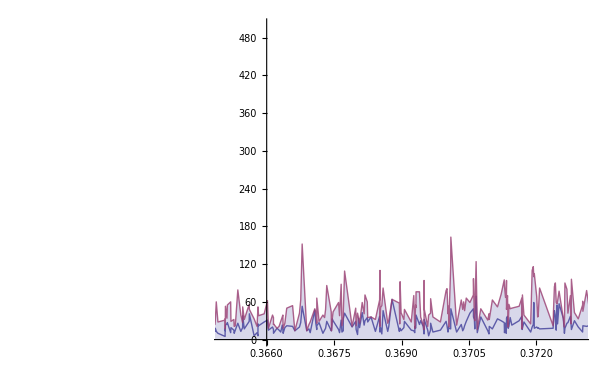

```mathematica
ListPlot[{formulaTable[myData[10]],formulaTable[myData[20]]}, 
			PlotRange->{{0.365,0.373},{0,500}}, 
			GridLines->{Join[Table[n,{n,0,0.6,0.01}],{{1/E,{Red, Thick}}}],Automatic},
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
                              Ticks->{All,All,All},  
                              PerformanceGoal->"Quality", 
                              Method->"QuasiNewton",
                              ImageSize->Large,
                              PlotStyle->Opacity[0.8],
                              Joined->True,
                             Filling->Join[{{1->Axis}},Table[{i+1->{i}},{i,1,7}]],
                             PlotMarkers->Automatic,
			 AxesLabel->{"formula(p,q,r,s)","countGood(p,q,r,s)"}
                               ]
```

```mathematica
myFormula[7,11,13,19]
```

0.367991

```mathematica
formulaInvValues = Table[{myFormulaInv[x[[1]]  ,x[[2]],x[[3]],x[[4]]], x[[5]] },{x,huge}]
```

{{5.27622,3},{5.13967,5},{4.96634,2},{4.90712,3},{4.653,4},{4.49608,10},{4.44247,3},{4.37972,4},{4.3275,8},{4.18156,2},{4.13043,4},{3.99113,9},{3.94354,7},{3.88784,5},{3.84149,12},{3.71193,8},{3.51971,11},{3.47774,18},{3.36045,13},{3.27349,40},{3.9224,8},{3.79012,12},{3.74493,11},{3.69204,10},{3.64801,16},{3.52499,8},{3.34244,21},{3.30258,21},{3.19121,61},{3.10862,268},{3.24428,102},{3.20559,55},{3.09749,596},{3.01732,6620},{2.91411,244453}}

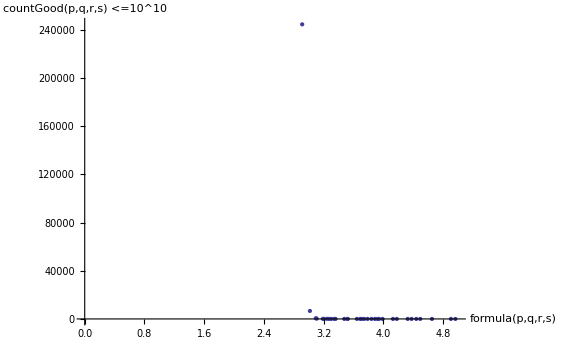

```mathematica
ListPlot[formulaInvValues, 
			PlotRange->{{0,5},All}, 
			GridLines->{Join[Table[n,{n,0,10,0.5}],{{E,{Red,Thick}}}],Automatic},
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
                              Ticks->{All,All,All},  
                              PerformanceGoal->"Quality", 
                              Method->"QuasiNewton",
                              ImageSize->Large,
                              Mesh->None,
                               ColorFunction->"DarkRainbow",
			 AxesLabel->{"formula(p,q,r,s)","countGood(p,q,r,s) <=10^10"}
                               ]
```

```mathematica
Join[Table[n,{n,1,10,0.5}],{{E,{Red,Thick}}}]
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,{ⅇ,{RGBColor[1,0,0],Thickness[Large]}}}

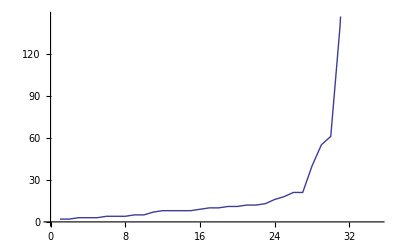

```mathematica
ListLinePlot[Sort[ Table[x[[5]] ,{x,huge}]]]
```

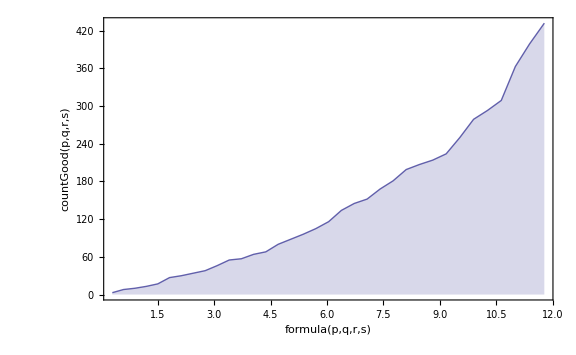

```mathematica
ListPlot[Accumulate[formulaTable[myData[10]]], 
                             PlotRange->All,
			LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
                              Ticks->{All,All,All},  
                              PerformanceGoal->"Quality", 
                              Method->"QuasiNewton",
                              ImageSize->Large,
                              PlotStyle->Opacity[0.8],
                              Joined->True,
                             Filling->Axis,
                             Frame->True,
			 AxesLabel->{"formula(p,q,r,s)","countGood(p,q,r,s)"}
                               ]
```